```mathematica
Clear["Global`*"]
```

Problem 1

```mathematica
v=r x^2+σ y^2 + σ(z-2r)^2;
dv=-2σ(rx^2+y^2+b ((z-r)^2-r^2));
```

```mathematica
v/.{σ->1,b->1}
dv/.{σ->1,b->1}
```

r x^2+y^2+(-2 r+z)^2

-2 (-r^2+rx^2+y^2+(-r+z)^2)

```mathematica
r=1;
eq1=r x^2+y^2+(-2 r+z)^2==c;
eq2=-2 (-r^2+r x^2+y^2+(-r+z)^2)==1;
s1=Solve[eq1,z];
s2=Solve[eq2,z];
Manipulate[Plot3D[{2-√(c-x^2-y^2),2+√(c-x^2-y^2),1/2 (2-√2 √(1-2 x^2-2 y^2)),1/2 (2+√2 √(1-2 x^2-2 y^2))},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.5],AxesLabel->Automatic],{c,-1,10}]
```

```mathematica
(* As we can see, for some values of c, the smaller ellipse will not be trapped in in the larger ellipse. *)
;
```

```mathematica
(* Top view of trapped ellipse. *)
;
```

```mathematica
(* Front view of trapped ellipse. *)
;
```

Problem 2

```mathematica
a=0;
dx1=y+a x;
dy1=x-x^2;

eqsol1=Solve[dx1==0,y]
eqsol2=Solve[dy1==0,x]

p1={eqsol1/.eqsol2[[1]],eqsol2[[1]]}

df1=({{D[dx1,x], D[dx1,y]}, {D[dy1,x], D[dy1,y]}})/.eqsol2[[1]]
eval1=Eigenvalues[df1]
evec1=Eigenvectors[df1]
```

{{y→0}}

{{x→0},{x→1}}

{{{y→0}},{x→0}}

{{0,1},{1,0}}

{-1,1}

{{-1,1},{1,1}}

```mathematica
p2={eqsol1/.eqsol2[[2]],eqsol2[[2]]}

df2=({{D[dx,x], D[dx,y]}, {D[dy,x], D[dy,y]}})/.eqsol2[[2]]
eval2=Eigenvalues[df2]
evec2=Eigenvectors[df2]
```

{{{y→0}},{x→1}}

{{0,0},{0,0}}

{0,0}

{{0,1},{1,0}}

```mathematica
ode=dy/dx;
(* ode is separable and the solution is below *)
y^2==x^2-2/3 x^3+k ;
(* Desmos plot input *)
-Graphics-;
(* Homoclinic path occurs at k==0. *)
-Graphics-;
```

```mathematica
dx2=y+A x;
dy2=x-x^2;

eqsol3=Solve[dx2==0,y]
eqsol4=Solve[dy2==0,x]

p3={eqsol3/.eqsol4[[1]],eqsol4[[1]]}

df3=({{D[dx2,x], D[dx2,y]}, {D[dy2,x], D[dy2,y]}})/.eqsol2[[1]]
eval3=Eigenvalues[df3]
evec3=Eigenvectors[df3]
```

{{y→-A x}}

{{x→0},{x→1}}

{{{y→0}},{x→0}}

{{A,1},{1,0}}

{1/2 (A-√(4+A^2)),1/2 (A+√(4+A^2))}

{{1/2 (A-√(4+A^2)),1},{1/2 (A+√(4+A^2)),1}}

```mathematica
p4={eqsol3/.eqsol4[[2]],eqsol4[[2]]}

df4=({{D[dx2,x], D[dx2,y]}, {D[dy2,x], D[dy2,y]}})/.eqsol4[[2]]
eval4=Eigenvalues[df4]
evec4=Eigenvectors[df4]
```

{{{y→-A}},{x→1}}

{{A,1},{-1,0}}

{1/2 (A-√(-4+A^2)),1/2 (A+√(-4+A^2))}

{{1/2 (-A+√(-4+A^2)),1},{1/2 (-A-√(-4+A^2)),1}}

To summarize what we have so far, we have four different Eigenvalues to the matrices above, namely λ=1/2(A±√(4+A^2)) and λ=1/2(-A±√(-4+A^2)).
The second set of Eigenvalues leave us with some different possibilities that A can be, namely A<0, A=0, 0<A<2, A=2, A>2 that will give us different plots.

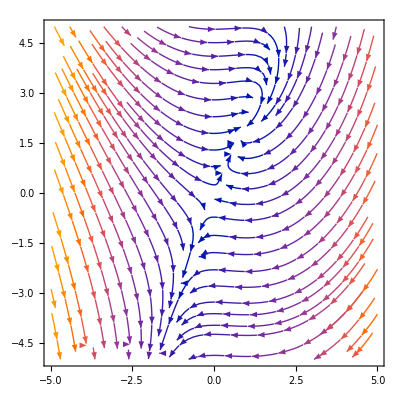

```mathematica
(* Case for A<0. *)
(* Note that for this case, we have a stable node. *)
StreamPlot[{dx2/.A->-2,dy2/.A->-2},{x,-5,5},{y,-5,5}]
```

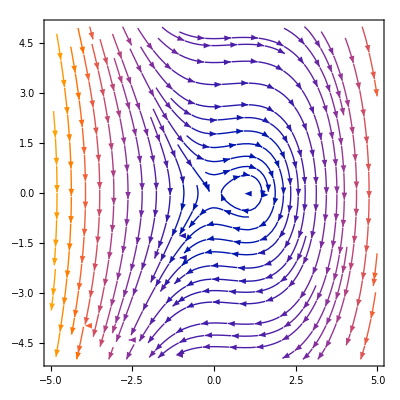

```mathematica
(* Case for A==0. *)
(* Note that for this case, we have a center. *)
StreamPlot[{dx2/.A->0,dy2/.A->0},{x,-5,5},{y,-5,5}]
```

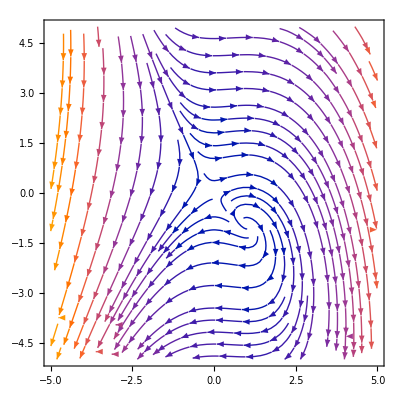

```mathematica
(* Case for 0<A<2. *)
(* Note that for this case, we have a unstable focus. *)
StreamPlot[{dx2/.A->1,dy2/.A->1},{x,-5,5},{y,-5,5}]
```

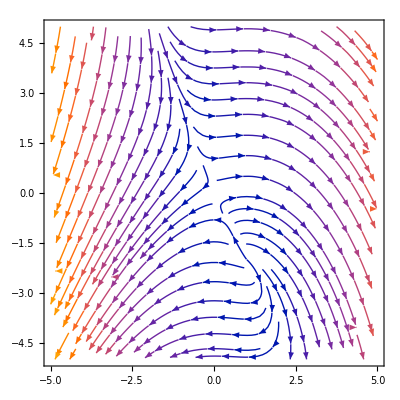

```mathematica
(* Case for A==2. *)
(* Note that for this case, we have a unstable node. *)
StreamPlot[{dx2/.A->2,dy2/.A->2},{x,-5,5},{y,-5,5}]
```

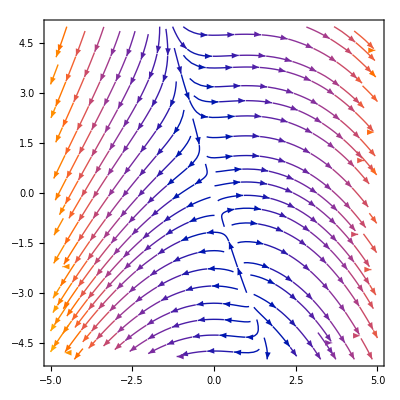

```mathematica
(* Case for A>2. *)
(* Note that for this case, we have a unstable node. *)
StreamPlot[{dx2/.A->3,dy2/.A->3},{x,-5,5},{y,-5,5}]
```